Singular value distribution (eigenvalues of √(HH^+)) for the GinUE

```mathematica
n = 40;singev={};Sprd={};
```

```mathematica
Monitor[For[i=1,i<5001,i++,{
(*ev=RandomReal[{-1,1},n]+ⅈ RandomReal[{-1,1},n];*)
H0=RandomVariate[NormalDistribution[0,1/√2],{n,n}]+ⅈ RandomVariate[NormalDistribution[0,1/√2],{n,n}] ;
ev=√Eigenvalues[H0.ConjugateTranspose[H0]];
(*singev=Join[singev,ev];*)
sev = Sort[ev];
spr=Table[(sev[[j+2]]-sev[[j+1]])/(sev[[j+1]]-sev[[j]]),{j,1,n-2}];
rtil =Min[spr,1/spr];
Sprd=Append[Sprd,rtil];
}],i]
```

```mathematica
rtil
```

0.177616

```mathematica
singev
```

{30.222,15.8192,12.9628,10.4016,8.21801,7.79928,7.27352,-6.55373,5.41825,-4.58046,99980,-4.54312,3.94917,3.61926,-3.57692,-2.40906,2.1213,-1.83934,-1.43103,1.02566,-0.618838}
 |  |  |  |

Normal Spacing Ratios of GUE

```mathematica
n = 100;singev={};Sprd={};Sprtil={};
```

```mathematica
Monitor[For[i=1,i<5001,i++,{
GUE=RandomVariate[GaussianUnitaryMatrixDistribution[n]] ;
ev=Eigenvalues[GUE];
singev=Join[singev,ev];
sev = Sort[ev];
rr=Table[(sev[[j+2]]-sev[[j+1]])/(sev[[j+1]]-sev[[j]]),{j,1,n-2}];
Sprd=Join[Sprd,rr];
Sprtil=Join[Sprtil,Table[Min[rr[[j]],1/rr[[j]]],{j,1,n-2}]];
}],i]
```

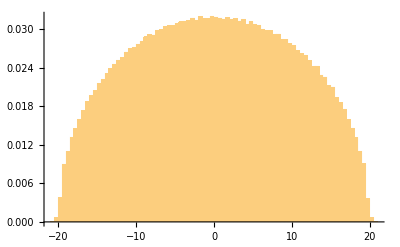

```mathematica
Show[Histogram[singev,60,"PDF",PlotRange->All]]
```

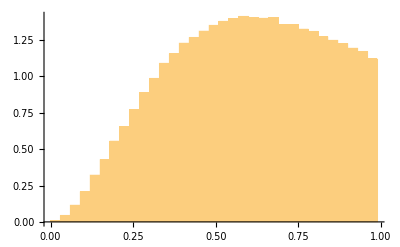

```mathematica
Histogram[Flatten[Sprtil],{0,1,0.03},"PDF"]
```

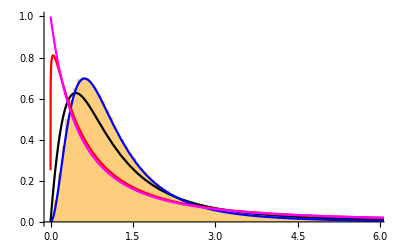

```mathematica
Show[Histogram[Flatten[Sprd],{0,6,0.07},"PDF"],Plot[{p1[r],p2[r],psp[r,0.1],1/(1+r)^2},{r,0,7},PlotRange->All,PlotStyle->{Black,Blue,Red,Magenta}]]
```

```mathematica
(*GinUE- GinOE crossover using the Pandey Mehta Hamiltonian*)
```

```mathematica
n = 50;singev={};Sprd={};λ= 0.0;Sprtil={};minev={};
```

```mathematica
Monitor[For[i=1,i<20001,i++,{
H1=RandomVariate[NormalDistribution[0,1/√2],{n,n}]; (*GinOE*)
H2=RandomVariate[NormalDistribution[0,1/√2],{n,n}]+ⅈ RandomVariate[NormalDistribution[0,1/√2],{n,n}];(*GinUE*)
H=1/(√(1+λ^2))H1+λ/(√(1+λ^2)) H2;
ev=√Eigenvalues[H.ConjugateTranspose[H]];
minev= Append[minev,Min[ev]];(*Smallest of the singular values*)
singev=Join[singev,ev];
sev = Sort[ev];
rr=Table[(sev[[j+2]]-sev[[j+1]])/(sev[[j+1]]-sev[[j]]),{j,1,n-2}];(*Adjacent level spacing ratios of the singular values*)
Sprd=Join[Sprd,rr];
Sprtil=Join[Sprtil,Table[Min[rr[[j]],1/rr[[j]]],{j,1,n-2}]];(*Adjacent level spacing ratios (of the other kind) of the singular values*)
}],i]
```

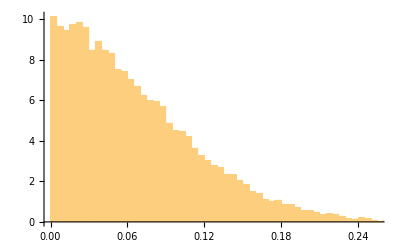

```mathematica
Histogram[Chop[minev],60,"PDF"]
```

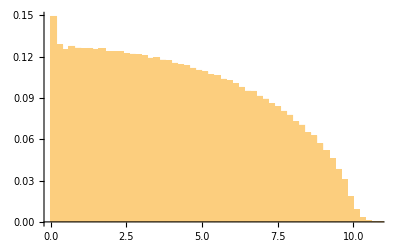

```mathematica
Histogram[Chop[singev],60,"PDF"]
```

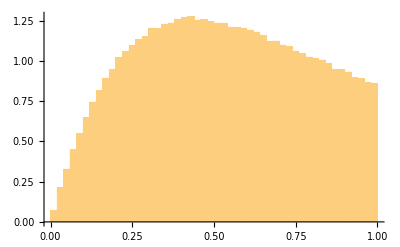

```mathematica
Histogram[Flatten[Sprtil],{0,1,0.02},"PDF"]
```

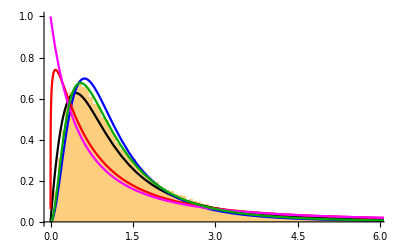

```mathematica
Show[Histogram[Chop[Sprd],{0,6,0.07},"PDF"],Plot[{p1[r],p2[r],psp[r,0.2],1/(1+r)^2,pλ[0.4,r]},{r,0,7},PlotRange->All,PlotStyle->{Black,Blue,Red,Magenta,Darker[Green]}]]
```

```mathematica
prt[λ_]:=Integrate[2pλ[λ,r]HeavisideTheta[1-r],{r,0,∞},Assumptions->λ>0]
```

```mathematica
g[η_,ζ_]:=(ζ(5 η^2+3 ζ^2))/(η^4(η^2+ζ^2)^2)+3/η^5 ArcTan[ζ/η];a[r_]:=√(1/6*(1+r+r^2));b[λ_]:=1/(2 √2 λ);bα[α_]:=√((1-α^2)/(8 α^2));
```

```mathematica
pλ[λ_,r_]:=(r (1+r))/(16 √6 π)(1+λ^2)^(3/2)(g[a[r],b[λ]]+g[a[r],b[λ]r]-g[a[r],b[λ](r+1)]);
```